```mathematica
Pt[x1_,x2_]:=-t x1 - Log[1 - x1] - Log[1-x2]-Log[x1]-Log[x2]
```

```mathematica
Solve[D[Pt[x1,x2],x1]==0,x1]
```

{{x1→-(2-t+√(4+t^2))/(2 t)},{x1→(-2+t+√(4+t^2))/(2 t)}}

```mathematica
Solve[D[Pt[x1,x2],x2]==0,x2]
```

{{x2→1/2}}

```mathematica
D[Pt[x1,x2],x2]==0
```

1/(1-x2)-1/x2==0

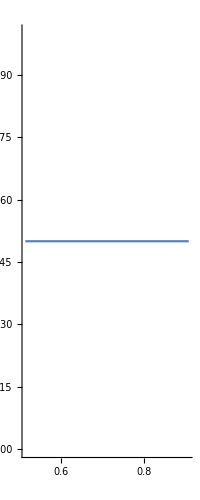

```mathematica
ParametricPlot[{(-2+t+√(4+t^2))/(2 t),1/2},{t,.1,10}]
```

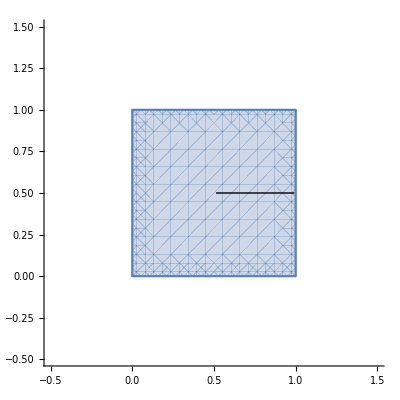

```mathematica
Show[RegionPlot[x1≥0&&x2≥0&&x1 -1≤0&&x2-1≤0,{x1,-.5,1.5},{x2,-.5,1.5},Frame->False,Axes->True],ParametricPlot[{(-2+t+√(4+t^2))/(2 t),1/2},{t,.1,120},PlotStyle->{Black,Thick}]]
```

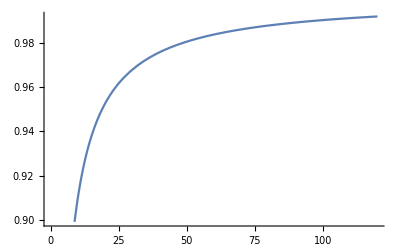

```mathematica
Plot[(-2+t+√(4+t^2))/(2 t),{t,0,120}]
```

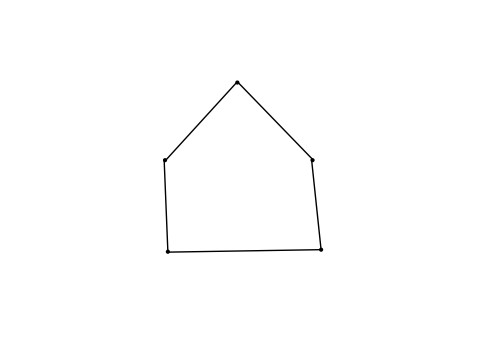

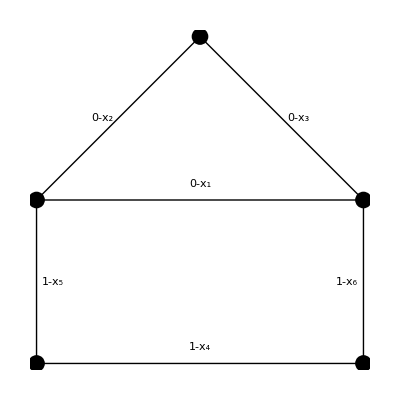

```mathematica
Graphics[{Line[{{0,0},{0,.5},{.5,1},{1,.5},{1,0},{0,0}}],Line[{{0,.5},{1,.5}}],{PointSize[.03],Point[{{0,0},{0,.5},{.5,1},{1,.5},{1,0}}]},Text["0-x_1",{.5,.55}],Text["0-x_2",{.2,.75}],Text["0-x_3",{.8,.75}],Text["1-x_4",{.5,.05}],Text["1-x_5",{.05,.25}],Text["1-x_6",{.95,.25}]}]
```